The Binomial Distribution

Calculating probability

Method 1:

```mathematica
Clear[X]
Probability[X==10,X\[Distributed]BinomialDistribution[20,0.4]]
```

0.117142

```mathematica
Probability[X≥10,X\[Distributed]BinomialDistribution[20,0.4]]
```

0.244663

```mathematica
Probability[10≤X≤14,X\[Distributed]BinomialDistribution[20,0.4]]
```

0.243051

Method 2:

```mathematica
PDF[BinomialDistribution[20,0.4],10]
```

0.117142

```mathematica
PDF[BinomialDistribution[20,0.4],{10,14,18}]
```

{0.117142,0.00485435,4.70041×10^-6}

Cumulative Distribution Function: Pr(X ≤ x) can be calculated using the CDF[dist, x] command. So Pr(X ≥ 10) = 1 - Pr(X ≤ 9) can be calculated using

```mathematica
1-CDF[BinomialDistribution[20,0.4],9]
```

0.244663

Conditional probability:

```mathematica
Probability[X≤10\[Conditioned]X≥5,X\[Distributed]BinomialDistribution[20,0.4]]
```

0.865632

Finding the minimum sample size

Example 1: Let X be a binomial random variable where p = 1/5. Find the smallest number of trials such that Pr(X ≥ 2) > 0.95.

```mathematica
Clear[f]
Clear[X]
f[n_]:=Probability[X≥2,X\[Distributed]BinomialDistribution[n,1/5]]
```

Option 1: Solve an inequality (Mathematica does not always give an answer).

```mathematica
Reduce[f[n]>0.95,n,Integers]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n∈ℤ&&n≥22.

Answer: n = 22.

```mathematica
f[22]//N
```

0.952038

Option 2: Use a table (‘guess-and-check’ values of n. Mathematica will always give an answer)

```mathematica
Table[{n,f[n]},{n,20,30}]//TableForm//N
```

20. | 0.930825
21. | 0.942354
22. | 0.952038
23. | 0.960155
24. | 0.966943
25. | 0.97261
26. | 0.977333
27. | 0.981262
28. | 0.984526
29. | 0.987234
30. | 0.989478

Answer: n = 22 by inspection.

Example 2: Let X be a binomial random variable where p = 0.6. Find the smallest number of trials such that Pr(X = 5) > 0.25.

```mathematica
Clear[f]
Clear[X]
f[n_]:=Probability[X==5,X\[Distributed]BinomialDistribution[n,0.6]]
```

Option 1: Solve an inequality (Mathematica does not always give an answer).

```mathematica
Reduce[f[n]>0.25,n,Integers]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n==7||n==8||n==9

Option 2: Use a table (‘guess-and-check’ values of n. Mathematica will always give an answer)

```mathematica
Table[{n,f[n]},{n,1,10}]//TableForm//N
```

1. | 0.
2. | 0.
3. | 0.
4. | 0.
5. | 0.07776
6. | 0.186624
7. | 0.261274
8. | 0.278692
9. | 0.250823
10. | 0.200658

Example 3: Let X be a binomial random variable where p = 7/10. Find the smallest number of trials such that Pr(X ≥ 50) > 0.99.

Option 1: Solve an inequality (Mathematica does not always give an answer).

```mathematica
Clear[X,g]
g[n_]:=Probability[X≥50,X\[Distributed]BinomialDistribution[n,7/10]]
```

```mathematica
Reduce[g[n]>0.99,n]//N
```

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[(Piecewise[{{BetaRegularized[0.7,50.,-49.+n], 49.<n}, {0., True}}])>0.99,n]

Mathematica does not give an answer.

Option 2: Use a table (‘trial-and-error’ with values of n) (Mathematica will always give an answer)

```mathematica
Table[{n,g[n]},{n,80,100}]//TableForm//N
```

80. | 0.941252
81. | 0.957147
82. | 0.969217
83. | 0.978215
84. | 0.984805
85. | 0.989549
86. | 0.99291
87. | 0.995253
88. | 0.996863
89. | 0.997952
90. | 0.99868
91. | 0.999159
92. | 0.99947
93. | 0.99967
94. | 0.999796
95. | 0.999876
96. | 0.999925
97. | 0.999955
98. | 0.999973
99. | 0.999984
100. | 0.999991

Answer: n = 86 by inspection.

Finding an unknown probability

Example 4: Let X be a binomial random variable where n = 100. Find, correct to four decimal places, the minimum value of p such that Pr(X ≥ 34) > 0.95.

```mathematica
Clear[f,X,p]
f[p_]:=Probability[X≥34,X\[Distributed]BinomialDistribution[100,p]]
```

Solve an inequality (Mathematica does not always give an answer).

```mathematica
Reduce[f[p]>0.95,p,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Reduce::fexp: Warning: Reduce used FunctionExpand to transform the system. Since FunctionExpand transformation rules are only generically correct, the solution set might have been altered.

BetaRegularized[p,34,67]∈ℝ&&(p<-0.12944||p>0.415454)

Check for rounding:

```mathematica
f[0.4155]
f[0.4154]
```

0.950095

0.949887

Mean and variance

Mean:

Method 1: Use the formula np.

Method 2:

```mathematica
Mean[BinomialDistribution[20,0.4]]
```

8.

Variance:

Method 1: Use the formula np(1-p).

Method 2:

```mathematica
Variance[BinomialDistribution[20,0.4]]
```

4.8

Constructing a table of values

```mathematica
Clear[X]
Table[{X,PDF[BinomialDistribution[10,0.4],X]},{X,0,10}]//TableForm
```

0 | 0.00604662
1 | 0.0403108
2 | 0.120932
3 | 0.214991
4 | 0.250823
5 | 0.200658
6 | 0.111477
7 | 0.0424673
8 | 0.0106168
9 | 0.00157286
10 | 0.000104858

Plotting a binomial distribution

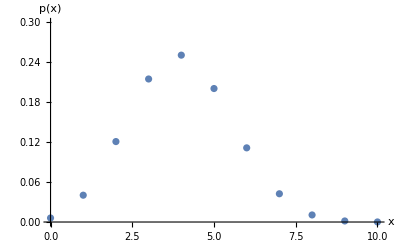

```mathematica
ListPlot[Table[{X,PDF[BinomialDistribution[10,0.4],X]},{X,0,10}],AxesLabel->{x,"p(x)"},PlotRange->{0,0.3}]
```

```mathematica
ListPlot[Table[{X,PDF[BinomialDistribution[20,0.9],X]},{X,0,20}],AxesLabel->{x,"p(x)"},
Filling->Axis,PlotStyle->{Directive[Red]},FillingStyle->{Directive[Thick]},PlotRange->{0,0.3}]
```

Note this is skewed LEFT

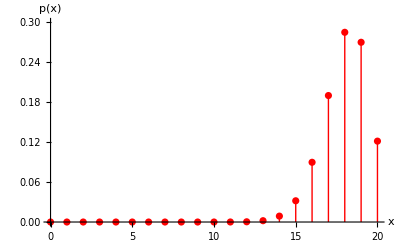

```mathematica
ListPlot[Table[{X,PDF[BinomialDistribution[20,0.5],X]},{X,0,20}],AxesLabel->{x,"p(x)"},
Filling->Axis,PlotStyle->{Directive[Red]},FillingStyle->{Directive[Thick]},PlotRange->{0,0.3}]
```

Symmetric but not “bell curve” because it is discrete

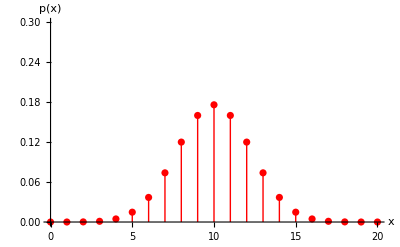

```mathematica
ListPlot[Table[{X,PDF[BinomialDistribution[200,0.1],X]},{X,0,200}],AxesLabel->{x,"p(x)"},
Filling->Axis,PlotStyle->{Directive[Red]},FillingStyle->{Directive[Thick]},PlotRange->{0,0.08}]
```

Still discrete

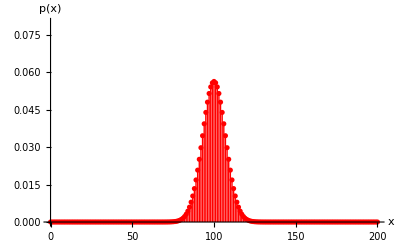

large amount of trials can create illusion of continuity and symmetry